## First have a look with 3 edges

```mathematica
ThreeEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==3]&]
```

{28431,26973,26487,26325,26271,26253,26247,26245,22599,22113,21951,21897,21879,21873,21871,20655,20493,20439,20421,20415,20413,20007,19953,19935,19929,19927,19791,19773,19767,19765,19719,19713,19711,19695,19693,19687,9477,8991,8829,8775,8757,8751,8749,7533,7371,7317,7299,7293,7291,6885,6831,6813,6807,6805,6669,6651,6645,6643,6597,6591,6589,6573,6571,6565,3159,2997,2943,2925,2919,2917,2511,2457,2439,2433,2431,2295,2277,2271,2269,2223,2217,2215,2199,2197,2191,1053,999,981,975,973,837,819,813,811,765,759,757,741,739,733,351,333,327,325,279,273,271,255,253,247,117,111,109,93,91,85,39,37,31,13}

```mathematica
Sort[Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[allGraphs5[28431,"colofour"]]]],#1[[1]]>#2[[1]]&]
```

{{4,1},{3,7},{2,10},{1,2}}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,ThreeEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{3,9},{4,7},{5,1}},-Graphics-26487},10}
{{{{2,2},{3,10},{4,7},{5,1}},-Graphics-28431},110}

## Now have a look with 4 edges

```mathematica
FourEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==4]&]
```

{29160,28674,28512,28458,28440,28434,28432,27216,27054,27000,26982,26976,26974,26568,26514,26496,26490,26488,26352,26334,26328,26326,26280,26274,26272,26256,26254,26248,22842,22680,22626,22608,22602,22600,22194,22140,22122,22116,22114,21978,21960,21954,21952,21906,21900,21898,21882,21880,21874,20736,20682,20664,20658,20656,20520,20502,20496,20494,20448,20442,20440,20424,20422,20416,20034,20016,20010,20008,19962,19956,19954,19938,19936,19930,19800,19794,19792,19776,19774,19768,19722,19720,19714,19696,9720,9558,9504,9486,9480,9478,9072,9018,9000,8994,8992,8856,8838,8832,8830,8784,8778,8776,8760,8758,8752,7614,7560,7542,7536,7534,7398,7380,7374,7372,7326,7320,7318,7302,7300,7294,6912,6894,6888,6886,6840,6834,6832,6816,6814,6808,6678,6672,6670,6654,6652,6646,6600,6598,6592,6574,3240,3186,3168,3162,3160,3024,3006,3000,2998,2952,2946,2944,2928,2926,2920,2538,2520,2514,2512,2466,2460,2458,2442,2440,2434,2304,2298,2296,2280,2278,2272,2226,2224,2218,2200,1080,1062,1056,1054,1008,1002,1000,984,982,976,846,840,838,822,820,814,768,766,760,742,360,354,352,336,334,328,282,280,274,256,120,118,112,94,40}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,FourEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{3,6},{4,6},{5,1}},-Graphics-28674},70}
{{{{2,1},{3,7},{4,6},{5,1}},-Graphics-29160},125}
{{{{2,2},{3,7},{4,6},{5,1}},-Graphics-26334},15}

## Now have a look with 5 edges

```mathematica
FiveEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==5]&]
```

{29403,29241,29187,29169,29163,29161,28755,28701,28683,28677,28675,28539,28521,28515,28513,28467,28461,28459,28443,28441,28435,27297,27243,27225,27219,27217,27081,27063,27057,27055,27009,27003,27001,26985,26983,26977,26595,26577,26571,26569,26523,26517,26515,26499,26497,26491,26361,26355,26353,26337,26335,26329,26283,26281,26275,26257,22923,22869,22851,22845,22843,22707,22689,22683,22681,22635,22629,22627,22611,22609,22603,22221,22203,22197,22195,22149,22143,22141,22125,22123,22117,21987,21981,21979,21963,21961,21955,21909,21907,21901,21883,20763,20745,20739,20737,20691,20685,20683,20667,20665,20659,20529,20523,20521,20505,20503,20497,20451,20449,20443,20425,20043,20037,20035,20019,20017,20011,19965,19963,19957,19939,19803,19801,19795,19777,19723,9801,9747,9729,9723,9721,9585,9567,9561,9559,9513,9507,9505,9489,9487,9481,9099,9081,9075,9073,9027,9021,9019,9003,9001,8995,8865,8859,8857,8841,8839,8833,8787,8785,8779,8761,7641,7623,7617,7615,7569,7563,7561,7545,7543,7537,7407,7401,7399,7383,7381,7375,7329,7327,7321,7303,6921,6915,6913,6897,6895,6889,6843,6841,6835,6817,6681,6679,6673,6655,6601,3267,3249,3243,3241,3195,3189,3187,3171,3169,3163,3033,3027,3025,3009,3007,3001,2955,2953,2947,2929,2547,2541,2539,2523,2521,2515,2469,2467,2461,2443,2307,2305,2299,2281,2227,1089,1083,1081,1065,1063,1057,1011,1009,1003,985,849,847,841,823,769,363,361,355,337,283,121}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,FiveEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{3,3},{4,5},{5,1}},-Graphics-28755},30}
{{{{3,4},{4,5},{5,1}},-Graphics-29403},150}
{{{{3,5},{4,5},{5,1}},-Graphics-26329},12}
{{{{2,1},{3,5},{4,5},{5,1}},-Graphics-28461},60}

## 6 edges

```mathematica
SixEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==6]&]
```

{29484,29430,29412,29406,29404,29268,29250,29244,29242,29196,29190,29188,29172,29170,29164,28782,28764,28758,28756,28710,28704,28702,28686,28684,28678,28548,28542,28540,28524,28522,28516,28470,28468,28462,28444,27324,27306,27300,27298,27252,27246,27244,27228,27226,27220,27090,27084,27082,27066,27064,27058,27012,27010,27004,26986,26604,26598,26596,26580,26578,26572,26526,26524,26518,26500,26364,26362,26356,26338,26284,22950,22932,22926,22924,22878,22872,22870,22854,22852,22846,22716,22710,22708,22692,22690,22684,22638,22636,22630,22612,22230,22224,22222,22206,22204,22198,22152,22150,22144,22126,21990,21988,21982,21964,21910,20772,20766,20764,20748,20746,20740,20694,20692,20686,20668,20532,20530,20524,20506,20452,20046,20044,20038,20020,19966,19804,9828,9810,9804,9802,9756,9750,9748,9732,9730,9724,9594,9588,9586,9570,9568,9562,9516,9514,9508,9490,9108,9102,9100,9084,9082,9076,9030,9028,9022,9004,8868,8866,8860,8842,8788,7650,7644,7642,7626,7624,7618,7572,7570,7564,7546,7410,7408,7402,7384,7330,6924,6922,6916,6898,6844,6682,3276,3270,3268,3252,3250,3244,3198,3196,3190,3172,3036,3034,3028,3010,2956,2550,2548,2542,2524,2470,2308,1092,1090,1084,1066,1012,850,364}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,SixEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{4,4},{5,1}},-Graphics-28764},5}
{{{{3,2},{4,4},{5,1}},-Graphics-29484},135}
{{{{3,3},{4,4},{5,1}},-Graphics-28702},60}
{{{{2,1},{3,4},{4,4},{5,1}},-Graphics-28462},10}

## 7 edges

```mathematica
SevenEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==7]&]
```

{29511,29493,29487,29485,29439,29433,29431,29415,29413,29407,29277,29271,29269,29253,29251,29245,29199,29197,29191,29173,28791,28785,28783,28767,28765,28759,28713,28711,28705,28687,28551,28549,28543,28525,28471,27333,27327,27325,27309,27307,27301,27255,27253,27247,27229,27093,27091,27085,27067,27013,26607,26605,26599,26581,26527,26365,22959,22953,22951,22935,22933,22927,22881,22879,22873,22855,22719,22717,22711,22693,22639,22233,22231,22225,22207,22153,21991,20775,20773,20767,20749,20695,20533,20047,9837,9831,9829,9813,9811,9805,9759,9757,9751,9733,9597,9595,9589,9571,9517,9111,9109,9103,9085,9031,8869,7653,7651,7645,7627,7573,7411,6925,3279,3277,3271,3253,3199,3037,2551,1093}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,SevenEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{4,3},{5,1}},-Graphics-29493},20}
{{{{3,1},{4,3},{5,1}},-Graphics-29511},70}
{{{{3,2},{4,3},{5,1}},-Graphics-28759},30}

## 8 edges

```mathematica
EightEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==8]&]
```

{29520,29514,29512,29496,29494,29488,29442,29440,29434,29416,29280,29278,29272,29254,29200,28794,28792,28786,28768,28714,28552,27336,27334,27328,27310,27256,27094,26608,22962,22960,22954,22936,22882,22720,22234,20776,9840,9838,9832,9814,9760,9598,9112,7654,3280}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,EightEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{4,2},{5,1}},-Graphics-29520},30}
{{{{3,1},{4,2},{5,1}},-Graphics-29488},15}

## 9 edges

```mathematica
NineEdges = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==9]&]
```

{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841}

```mathematica
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,NineEdges}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
```

{{{{4,1},{5,1}},-Graphics-29523},10}

## All edges

```mathematica
Column[
Table[
Labeled[
With[
{relevant = Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==edges]&]},
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs5[k,"colofour"]]]]],Labeled[allGraphs5[k,"graph"],k]},
{k,relevant}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
],
Style[edges,Red,48,Bold],
Top
],
{edges,0,10}
]
]
```

{{{{1,1},{2,15},{3,25},{4,10},{5,1}},-Graphics-0},1}0
{{{{2,8},{3,19},{4,9},{5,1}},-Graphics-19683},10}1
{{{{2,4},{3,14},{4,8},{5,1}},-Graphics-26244},45}2
{{{{3,9},{4,7},{5,1}},-Graphics-26487},10}
{{{{2,2},{3,10},{4,7},{5,1}},-Graphics-28431},110}3
{{{{3,6},{4,6},{5,1}},-Graphics-28674},70}
{{{{2,1},{3,7},{4,6},{5,1}},-Graphics-29160},125}
{{{{2,2},{3,7},{4,6},{5,1}},-Graphics-26334},15}4
{{{{3,3},{4,5},{5,1}},-Graphics-28755},30}
{{{{3,4},{4,5},{5,1}},-Graphics-29403},150}
{{{{3,5},{4,5},{5,1}},-Graphics-26329},12}
{{{{2,1},{3,5},{4,5},{5,1}},-Graphics-28461},60}5
{{{{4,4},{5,1}},-Graphics-28764},5}
{{{{3,2},{4,4},{5,1}},-Graphics-29484},135}
{{{{3,3},{4,4},{5,1}},-Graphics-28702},60}
{{{{2,1},{3,4},{4,4},{5,1}},-Graphics-28462},10}6
{{{{4,3},{5,1}},-Graphics-29493},20}
{{{{3,1},{4,3},{5,1}},-Graphics-29511},70}
{{{{3,2},{4,3},{5,1}},-Graphics-28759},30}7
{{{{4,2},{5,1}},-Graphics-29520},30}
{{{{3,1},{4,2},{5,1}},-Graphics-29488},15}8
{{{{4,1},{5,1}},-Graphics-29523},10}9
{{{{5,1}},-Graphics-29524},1}10

```mathematica
PaintEdges[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,   blueEdges, blueVertices, g, edgeSymbols, otherEdges, labels, nodes},
edgeSymbols=Select[ListofVars[form2],StringCount[SymbolName[#],"x"]==2&];
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
g=Graph[vars,edges];
blueEdges=edges2;
blueVertices=Map[#[[2]]&,blueEdges];
otherEdges=Flatten[Join[Table[Descendents[g,{e}],{e,edgeSymbols}]]];
labels=Map[#[[1]]->Style[ #[[2]],Bold]&,Tally[otherEdges]];
nodes=Map[#[[1,1]]-> Part[{Red,Darker[Green],Blue,Darker[Red],Yellow,Purple},#[[2]]]&,Tally[otherEdges]];
otherEdges=Map[#[[1]]-> Part[{Red,Darker[Green],Blue,Darker[Red],Yellow,Purple},#[[2]]]&,Tally[otherEdges]];
Graph[vars,edges,
VertexLabels->Table[n->Rotate[SymbolToLabel[n],Pi/4],{n,vars}],
GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->otherEdges,
EdgeLabels->labels,
VertexStyle->Join[nodes,Map[#->Cyan&,blueVertices]],
ImageSize->720]
]
```

```mathematica
allGraphs5[26334,"colofour"]
```

v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5

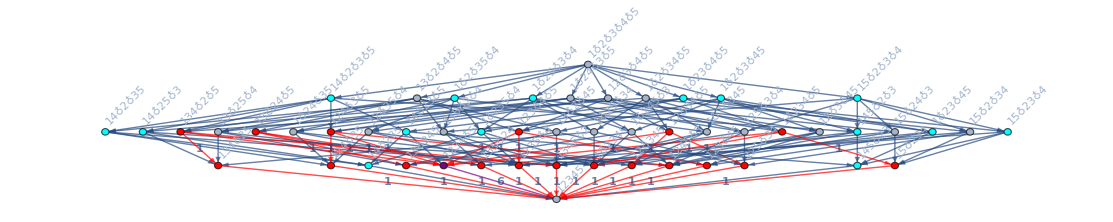

```mathematica
PaintEdges[K5Key, 26334, allGraphs5]
```